```mathematica
(*
Hofstadter RG flow equation solver and plotting
for arXiv:2204.13116
*)
```

```mathematica
(*Packages for plotting*)
Get["SciDraw`"]
Get["CustomTicks`"]
```

```mathematica
(*parameters*)
p=1;
q=3;
dph=0.8;
V0=1;  (*on-site interactions*)
V1=0; (*on-site interactions*)
```

```mathematica
(*build the Hamiltonian*)

T=1;
H[k_,p_,q_]:=DiagonalMatrix[Table[-2T Cos[k[[2]]+2Pi p s/q],{s,0,q-1}]]+DiagonalMatrix[Table[-T Exp[I k[[1]]],{s,0,q-2}],1]+DiagonalMatrix[{-T Exp[I  k[[1]]]},1-q] +DiagonalMatrix[Table[-T Exp[-I  k[[1]]],{s,0,q-2}],-1]+DiagonalMatrix[{-T Exp[-I  k[[1]]]},q-1] //N


(*build diagonalizing transformation u(k) with the sublattice and the band indices*)


Umat[k_,p_,q_]:=Module[{vals,vecs,Umatrix},{vals,vecs} = Eigensystem[H[k,p,q]];Umatrix = Inverse[Transpose[(Normalize/@vecs)[[Ordering[vals]]]]];
DiagonalMatrix[Table[Exp[-I Arg[Umatrix[[j,1]]]],{j,1,q}]].Umatrix]
U=ConstantArray[0,{q,3}];
U[[1,3]]=Umat[{0,Pi/q},p,q];
U[[1,2]]=Umat[{-Pi/q,0},p,q];
U[[1,1]]=Umat[{0,-Pi/q},p,q];
For[l=1,l<q,l++,
For[v=-1,v<2,v++,
U[[Mod[l,q]+1,Mod[v,3,-1]+2]]=Table[U[[1,Mod[v,3,-1]+2]] [[Mod[m,q]+1,Mod[n+ModularInverse[p,q]*l,q]+1]],{m,0,q-1},{n,0,q-1}];
]
]
Clear[l,v]
```

```mathematica
(*define the patch momenta*)

P[q_,l_,v_]:={Mod[v+1,2]Pi/q,Mod[2l+v,2q]Pi/q}
```

```mathematica
(*function calculating the projected coupling constants, on-site only*)

CouplingConstant[p_,q_,band_,l_,u_,m_,v_,n_,w_]:=Sum[U[[Mod[l+n,q]+1,Mod[u+w,3,-1]+2]][[band+1,sublattice+1]]U[[Mod[-n,q]+1,Mod[-w,3,-1]+2]][[band+1,sublattice+1]]Conjugate[U[[Mod[-m ,q]+1,Mod[-v,3,-1]+2]][[band+1,sublattice+1]]]Conjugate[U[[Mod[l+m,q]+1,Mod[u+v,3,-1]+2]][[band+1,sublattice+1]]],{sublattice,0,q-1}]
```

```mathematica
(*function calculating the projected coupling constants with NN *)

CouplingConstant[p_,q_,band_,l_,u_,m_,v_,n_,w_]:=V0 Sum[U[[Mod[l+n,q]+1,Mod[u+w,3,-1]+2]][[band+1,sublattice+1]]U[[Mod[-n,q]+1,Mod[-w,3,-1]+2]][[band+1,sublattice+1]]Conjugate[U[[Mod[-m ,q]+1,Mod[-v,3,-1]+2]][[band+1,sublattice+1]]]Conjugate[U[[Mod[l+m,q]+1,Mod[u+v,3,-1]+2]][[band+1,sublattice+1]]],{sublattice,0,q-1}]+
V1 Sum[Cos[(P[q,-n,-w][[2]]-P[q,-m,-v][[2]])]U[[Mod[l+n,q]+1,Mod[u+w,3,-1]+2]][[band+1,sublattice+1]]U[[Mod[-n,q]+1,Mod[-w,3,-1]+2]][[band+1,sublattice+1]]Conjugate[U[[Mod[-m ,q]+1,Mod[-v,3,-1]+2]][[band+1,sublattice+1]]]Conjugate[U[[Mod[l+m,q]+1,Mod[u+v,3,-1]+2]][[band+1,sublattice+1]]],{sublattice,0,q-1}]+V1 Sum[Exp[I(P[q,-n,-w][[1]]-P[q,-m,-v][[1]])]U[[Mod[l+n,q]+1,Mod[u+w,3,-1]+2]][[band+1,sublattice+1]]U[[Mod[-n,q]+1,Mod[-w,3,-1]+2]][[band+1,Mod[sublattice+1,q]]]Conjugate[U[[Mod[-m ,q]+1,Mod[-v,3,-1]+2]][[band+1,Mod[sublattice+1,q]+1]]]Conjugate[U[[Mod[l+m,q]+1,Mod[u+v,3,-1]+2]][[band+1,sublattice+1]]],{sublattice,0,q-1}]/2+V1 Sum[Exp[-I(P[q,-n,-w][[1]]-P[q,-m,-v][[1]])]U[[Mod[l+n,q]+1,Mod[u+w,3,-1]+2]][[band+1,sublattice+1]]U[[Mod[-n,q]+1,Mod[-w,3,-1]+2]][[band+1,Mod[sublattice-1,q]+1]]Conjugate[U[[Mod[-m ,q]+1,Mod[-v,3,-1]+2]][[band+1,Mod[sublattice-1,q]+1]]]Conjugate[U[[Mod[l+m,q]+1,Mod[u+v,3,-1]+2]][[band+1,sublattice+1]]],{sublattice,0,q-1}]/2
```

```mathematica
(*functions*)

(*flowing coupling constants*)
g1:=Function[{i,j},ToExpression["gI"<>ToString[i]<>"c"<>ToString[j]<>"[t]"]];
g1p:=Function[{i,j},ToExpression["gIp"<>ToString[i]<>"c"<>ToString[j]<>"[t]"]];
g2:=Function[{i,j},ToExpression["gII"<>ToString[i]<>"c"<>ToString[j]<>"[t]"]];
g3:=Function[{i,j},ToExpression["gIII"<>ToString[i]<>"c"<>ToString[j]<>"[t]"]];
g4:=Function[{i,j},ToExpression["gIV"<>ToString[i]<>"c"<>ToString[j]<>"[t]"]];

(*coupling constant names, needed for plotting*)
g1v:=Function[{i,j},ToExpression["gI"<>ToString[i]<>"c"<>ToString[j]]];
g1pv:=Function[{i,j},ToExpression["gIp"<>ToString[i]<>"c"<>ToString[j]]];
g2v:=Function[{i,j},ToExpression["gII"<>ToString[i]<>"c"<>ToString[j]]];
g3v:=Function[{i,j},ToExpression["gIII"<>ToString[i]<>"c"<>ToString[j]]];
g4v:=Function[{i,j},ToExpression["gIV"<>ToString[i]<>"c"<>ToString[j]]];

(*flowing vertices*)
D0:=Function[i,ToExpression["DO"<>ToString[i]<>"[t]"]];
D1:=Function[i,ToExpression["DI"<>ToString[i]<>"[t]"]];
R:=Function[{i,j},ToExpression["R"<>ToString[i]<>"c"<>ToString[j]<>"[t]"]];
R0:=Function[{i,j},ToExpression["RO"<>ToString[i]<>"c"<>ToString[j]<>"[t]"]];
R1:=Function[{i,j},ToExpression["R1"<>ToString[i]<>"c"<>ToString[j]<>"[t]"]];
M:=Function[{i,j},ToExpression["M"<>ToString[i]<>"c"<>ToString[j]<>"[t]"]];
M0:=Function[{i,j},ToExpression["MO"<>ToString[i]<>"c"<>ToString[j]<>"[t]"]];
M1:=Function[{i,j},ToExpression["M1"<>ToString[i]<>"c"<>ToString[j]<>"[t]"]];

(*vertex names, needed for plotting*)
D0v:=Function[i,ToExpression["DO"<>ToString[i]]];
D1v:=Function[i,ToExpression["DI"<>ToString[i]]];
Rv:=Function[{i,j},ToExpression["R"<>ToString[i]<>"c"<>ToString[j]]];
R0v:=Function[{i,j},ToExpression["RO"<>ToString[i]<>"c"<>ToString[j]]];
R1v:=Function[{i,j},ToExpression["R1"<>ToString[i]<>"c"<>ToString[j]]];
Mv:=Function[{i,j},ToExpression["M"<>ToString[i]<>"c"<>ToString[j]]];
M0v:=Function[{i,j},ToExpression["MO"<>ToString[i]<>"c"<>ToString[j]]];
M1v:=Function[{i,j},ToExpression["M1"<>ToString[i]<>"c"<>ToString[j]]];


(*susceptibilities*)
χD0:=Function[i,ToExpression["χDO"<>ToString[i]<>"[t]"]];
χD1:=Function[i,ToExpression["χDI"<>ToString[i]<>"[t]"]];
χR:=Function[{i,j},ToExpression["χR"<>ToString[i]<>"c"<>ToString[j]<>"[t]"]];
χR0:=Function[{i,j},ToExpression["χRO"<>ToString[i]<>"c"<>ToString[j]<>"[t]"]];
χR1:=Function[{i,j},ToExpression["χR1"<>ToString[i]<>"c"<>ToString[j]<>"[t]"]];
χM:=Function[{i,j},ToExpression["χM"<>ToString[i]<>"c"<>ToString[j]<>"[t]"]];
χM0:=Function[{i,j},ToExpression["χMO"<>ToString[i]<>"c"<>ToString[j]<>"[t]"]];
χM1:=Function[{i,j},ToExpression["χM1"<>ToString[i]<>"c"<>ToString[j]<>"[t]"]];



χD0v:=Function[i,ToExpression["χDO"<>ToString[i]]];
χD1v:=Function[i,ToExpression["χDI"<>ToString[i]]];
χRv:=Function[{i,j},ToExpression["χR"<>ToString[i]<>"c"<>ToString[j]]];
χR0v:=Function[{i,j},ToExpression["χRO"<>ToString[i]<>"c"<>ToString[j]]];
χR1v:=Function[{i,j},ToExpression["χR1"<>ToString[i]<>"c"<>ToString[j]]];
χMv:=Function[{i,j},ToExpression["χM"<>ToString[i]<>"c"<>ToString[j]]];
χM0v:=Function[{i,j},ToExpression["χMO"<>ToString[i]<>"c"<>ToString[j]]];
χM1v:=Function[{i,j},ToExpression["χM1"<>ToString[i]<>"c"<>ToString[j]]];

(*file name function for exporting files*)
RGflowSolsFileNames:=Function[{p,q,dph,V0,V1,band},"RGflowSolp"<>ToString[p]<>"q"<>ToString[q]<>"dph"<>ToString[dph]<>"_V0"<>ToString[V0]<>"_V1"<>ToString[V1]<>"_band"<>ToString[band]<>".wdx"];
```

```mathematica
(* generate bare coupling constants *)
gBands=Table[{Table[CouplingConstant[p,q,band,0,0,m,0,n,0],{m,0,q-1},{n,0,q-1}],Table[CouplingConstant[p,q,band,0,0,m,1,n,1],{m,0,q-1},{n,0,q-1}],Table[CouplingConstant[p,q,band,0,1,m,0,n,0],{m,0,q-1},{n,0,q-1}],Table[CouplingConstant[p,q,band,0,1,m,0,n,-1],{m,0,q-1},{n,0,q-1}],Table[CouplingConstant[p,q,band,0,0,m,0,n,1],{m,0,q-1},{n,0,q-1}]},{band,0,q-1}];
```

```mathematica
(*(*Set up RG equations and BCs, Eq. (7) in main text and Eqs. (S7) and (S10) in the supplementary material*)*)

(*arrays of coupling constants with different L's*)
G1L=Table[0,q];
G1pL=Table[0,q];
G2L=Table[0,q];
G3L=Table[0,q];
G4L=Table[0,q];
G1L[[1]]=Table[g1[m,n],{m,0,q-1},{n,0,q-1}];
G1pL[[1]]=Table[g1p[m,n],{m,0,q-1},{n,0,q-1}];
G2L[[1]]=Table[g2[m,n],{m,0,q-1},{n,0,q-1}];
G3L[[1]]=Table[g3[m,n],{m,0,q-1},{n,0,q-1}];G4L[[1]]=Table[g4[m,n],{m,0,q-1},{n,0,q-1}];
For[L=1,L≤ q-1,L++,
G1L[[Mod[2p L,q]+1]]=Table[G1L[[1]][[Mod[m+p L,q]+1,Mod[n+p L,q]+1]],{m,0,q-1},{n,0,q-1}];
G1pL[[Mod[2p L,q]+1]]=Table[G1pL[[1]][[Mod[m+p L,q]+1,Mod[n+p L,q]+1]],{m,0,q-1},{n,0,q-1}];
G2L[[Mod[2p L,q]+1]]=Table[G2L[[1]][[Mod[m+p L,q]+1,Mod[n+p L,q]+1]],{m,0,q-1},{n,0,q-1}];
G3L[[Mod[2p L,q]+1]]=Table[G3L[[1]][[Mod[m+p L,q]+1,Mod[n+p L,q]+1]],{m,0,q-1},{n,0,q-1}];
G4L[[Mod[2p L,q]+1]]=Table[G4L[[1]][[Mod[m+p L,q]+1,Mod[n+p L,q]+1]],{m,0,q-1},{n,0,q-1}];]
Clear[L]

(*CDW combinations of coupling constants*)
GR00=Table[dph Sum[Exp[2Pi I m k/q](G2L[[Mod[l+m,q]+1]][[Mod[-m,q]+1,1]]-2G3L[[Mod[l-m,q]+1]][[1,Mod[-l,q]+1]]),{m,0,q-1}],{l,0,q-1},{k,0,q-1}];
GR10=Table[dph Sum[Exp[2Pi I m k/q](G4L[[Mod[l+m,q]+1]][[Mod[-l,q]+1,Mod[-l-m,q]+1]]-2G4L[[Mod[l-m,q]+1]][[1,Mod[-l,q]+1]]),{m,0,q-1}],{l,0,q-1},{k,0,q-1}];
GR11=Table[dph Sum[Exp[2Pi I m k/q](G2L[[Mod[l+m-1,q]+1]][[Mod[1-l,q]+1,Mod[1-l-m,q]+1]]-2G3L[[Mod[l+m-1,q]+1]][[Mod[1-l,q]+1,1]]),{m,0,q-1}],{l,0,q-1},{k,0,q-1}];
(*SDW combinations of coupling constants*)
GM00=Table[dph Sum[Exp[2Pi I m k/q]G2L[[Mod[l+m,q]+1]][[Mod[-m,q]+1,1]],{m,0,q-1}],{l,0,q-1},{k,0,q-1}];
GM10=Table[dph Sum[Exp[2Pi I m k/q]G4L[[Mod[l+m,q]+1]][[Mod[-l,q]+1,Mod[-l-m,q]+1]],{m,0,q-1}],{l,0,q-1},{k,0,q-1}];
GM11=Table[dph Sum[Exp[2Pi I m k/q]G2L[[Mod[l+m-1,q]+1]][[Mod[1-l,q]+1,Mod[1-l-m,q]+1]],{m,0,q-1}],{l,0,q-1},{k,0,q-1}];

GR=(GR00+GR11+Sqrt[(GR00+GR11)^2+4Abs[GR10]^2])/2;
GM=(GM00+GM11+Sqrt[(GM00+GM11)^2+4Abs[GM10]^2])/2;




(*arrays of vertices*)
D0L=Table[D0[m],{m,0,q-1}];
D1L=Table[D1[m],{m,0,q-1}];
RL=Table[R[m,n],{m,0,q-1},{n,0,q-1}];
ML=Table[M[m,n],{m,0,q-1},{n,0,q-1}];

(*arrays of suceptibilites*)
χD0L=Table[χD0[m],{m,0,q-1}];
χD1L=Table[χD1[m],{m,0,q-1}];
χRL=Table[χR[m,n],{m,0,q-1},{n,0,q-1}];
χML=Table[χM[m,n],{m,0,q-1},{n,0,q-1}];

(*lists of variables needed for DSolve*)
gList=Flatten[Join[Table[g1[m,n],{m,0,q-1},{n,0,q-1}],Table[g1p[m,n],{m,0,q-1},{n,0,q-1}],Table[g2[m,n],{m,0,q-1},{n,0,q-1}],Table[g3[m,n],{m,0,q-1},{n,0,q-1}],Table[g4[m,n],{m,0,q-1},{n,0,q-1}]]];
gVarList=Flatten[Join[Table[g1v[m,n],{m,0,q-1},{n,0,q-1}],Table[g1pv[m,n],{m,0,q-1},{n,0,q-1}],Table[g2v[m,n],{m,0,q-1},{n,0,q-1}],Table[g3v[m,n],{m,0,q-1},{n,0,q-1}],Table[g4v[m,n],{m,0,q-1},{n,0,q-1}]]];
vxList=Flatten[Join[D0L,D1L,RL,ML]];
vxVarList=Flatten[Join[Table[D0v[m],{m,0,q-1}],Table[D1v[m],{m,0,q-1}],Table[Rv[m,n],{m,0,q-1},{n,0,q-1}],Table[Mv[m,n],{m,0,q-1},{n,0,q-1}]]];
χvxList=Flatten[Join[χD0L,χD1L,χRL,χML]];
χvxVarList=Flatten[Join[Table[χD0v[m],{m,0,q-1}],Table[χD1v[m],{m,0,q-1}],Table[χRv[m,n],{m,0,q-1},{n,0,q-1}],Table[χMv[m,n],{m,0,q-1},{n,0,q-1}]]];
χvxList=Flatten[Join[χD0L,χD1L,χRL,χML]];
χvxVarList=Flatten[Join[Table[χD0v[m],{m,0,q-1}],Table[χD1v[m],{m,0,q-1}],Table[χRv[m,n],{m,0,q-1},{n,0,q-1}],Table[χMv[m,n],{m,0,q-1},{n,0,q-1}]]];

(*boundary conditions for vertices and susceptibility needed for DSolve*)
BCvxList=Flatten[Join[Table[Evaluate[D0L[[m+1]]/.{t-> 0}]==1 q m,{m,0,q-1}],Table[Evaluate[D1L[[m+1]]/.{t-> 0}]==2q m Exp[-2I  Pi/3],{m,0,q-1}],Table[Evaluate[RL[[m+1,n+1]]/.{t-> 0}]== 1,{m,0,q-1},{n,0,q-1}],Table[Evaluate[ML[[m+1,n+1]]/.{t-> 0}]== 1,{m,0,q-1},{n,0,q-1}]]];
χBCvxList=Flatten[Join[Table[Evaluate[χD0L[[m+1]]/.{t-> 0}]== 0,{m,0,q-1}],Table[Evaluate[χD1L[[m+1]]/.{t-> 0}]==0,{m,0,q-1}],Table[Evaluate[χRL[[m+1,n+1]]/.{t-> 0}]== 0,{m,0,q-1},{n,0,q-1}],Table[Evaluate[χML[[m+1,n+1]]/.{t-> 0}]== 0,{m,0,q-1},{n,0,q-1}]]];

(*RG flow equations for the coupling constants*)
RGflowEqsMod=Flatten[Join[Table[D[G1L[[1]][[m+1,n+1]],t]== -Sum[G1L[[1]][[m+1,k+1]]G1L[[1]][[k+1,n+1]]+G4L[[1]][[m+1,k+1]]Conjugate[G4L[[1]][[n+1,k+1]]],{k,0,q-1}],{m,0,q-1},{n,0,q-1}],Table[D[G1pL[[1]][[m+1,n+1]],t]== -Sum[G1pL[[1]][[m+1,k+1]]G1pL[[1]][[k+1,n+1]]+Conjugate[G4L[[1]][[k+1,m+1]]]G4L[[1]][[k+1,n+1]],{k,0,q-1}],{m,0,q-1},{n,0,q-1}],Table[D[G2L[[1]][[m+1,n+1]],t]== dph Sum[G2L[[Mod[n-k,q]+1]][[m+1,k+1]]G2L[[Mod[m-k,q]+1]][[k+1,n+1]]+Conjugate[G4L[[Mod[n-k,q]+1]][[k+1,Mod[m-1,q]+1]]]G4L[[Mod[m-k,q]+1]][[k+1,Mod[n-1,q]+1]],{k,0,q-1}],{m,0,q-1},{n,0,q-1}],Table[D[G3L[[1]][[m+1,n+1]],t]== dph Sum[-2(G3L[[Mod[m+n+k,q]+1]][[Mod[-n-k,q]+1,Mod[-m-k,q]+1]]G3L[[k+1]][[m+1,n+1]]+G4L[[Mod[m+n+k,q]+1]][[Mod[-n-k,q]+1,Mod[-m-k,q]+1]]Conjugate[G4L[[k+1]][[n+1,Mod[m-1,q]+1]]])+(G4L[[Mod[m+n+k,q]+1]][[Mod[-n-k,q]+1,Mod[-m-k,q]+1]]Conjugate[G4L[[k+1]][[n+1,Mod[-m-k,q]+1]]]+G3L[[Mod[m+n+k,q]+1]][[Mod[-n-k,q]+1,Mod[-m-k,q]+1]]G2L[[k+1]][[m+1,Mod[-n-k,q]+1]])+(G2L[[Mod[m+n+k,q]+1]][[Mod[-n-k,q]+1,Mod[-n,q]+1]]G3L[[k+1]][[m+1,n+1]]+G4L[[Mod[m+n+k,q]+1]][[Mod[-n-k,q]+1,Mod[-n-1,q]+1]]Conjugate[G4L[[k+1]][[n+1,Mod[m-1,q]+1]]]),{k,0,q-1}],{m,0,q-1},{n,0,q-1}],Table[D[G4L[[1]][[m+1,n+1]],t]== Sum[-G1L[[1]][[m+1,k+1]]G4L[[1]][[k+1,n+1]]-G4L[[1]][[m+1,k+1]]G1pL[[1]][[k+1,n+1]]+dph(G2L[[Mod[n-k,q]+1]][[Mod[k-m-n,q]+1,Mod[-n,q]+1]]G4L[[Mod[m-k,q]+1]][[k+1,n+1]]+G4L[[Mod[n-k,q]+1]][[m+1,k+1]]G2L[[Mod[m-k-1,q]+1]][[Mod[k+1,q]+1,Mod[n+1,q]+1]]-2(G4L[[Mod[m+n+k,q]+1]][[Mod[-n-k,q]+1,Mod[-m-k,q]+1]]G3L[[Mod[k-1,q]+1]][[Mod[1-k-m,q]+1,Mod[-n-k,q]+1]]+G3L[[Mod[m+n+k,q]+1]][[Mod[-n-k,q]+1,Mod[-m-k,q]+1]]G4L[[k+1]][[m+1,n+1]])+(G4L[[Mod[m+n+k,q]+1]][[Mod[-n-k,q]+1,Mod[-m-k,q]+1]]G2L[[Mod[k-1,q]+1]][[Mod[-m-k+1,q]+1,Mod[n+1,q]+1]]+G3L[[Mod[m+n+k,q]+1]][[Mod[-n-k,q]+1,Mod[-m-k,q]+1]]G4L[[k+1]][[Mod[-m-k,q]+1,n+1]])+(G2L[[Mod[m+n+k,q]+1]][[Mod[-n-k,q]+1,Mod[-n,q]+1]]G4L[[k+1]][[m+1,n+1]]+G4L[[Mod[m+n+k,q]+1]][[Mod[-n-k,q]+1,Mod[-n-1,q]+1]]G3L[[Mod[k-1,q]+1]][[Mod[1-k-m,q]+1,Mod[-n-k,q]+1]])),{k,0,q-1}],{m,0,q-1},{n,0,q-1}]]];


(*RG flow equations for the vertices*)
RGvxFlowEqsMod=
Flatten[Join[Table[D[D0L[[m+1]],t]== -Sum[G1L[[1]][[n+1,m+1]]D0L[[n+1]]+Conjugate[G4L[[1]][[m+1,n+1]]]D1L[[n+1]],{n,0,q-1}],{m,0,q-1}],Table[D[D1L[[m+1]],t]== -Sum[G1pL[[1]][[n+1,m+1]]D1L[[n+1]]+G4L[[1]][[n+1,m+1]]D0L[[n+1]],{n,0,q-1}],{m,0,q-1}],Table[D[RL[[l+1,k+1]],t]==GR[[l+1,k+1]] RL[[l+1,k+1]],{l,0,q-1},{k,0,q-1}],Table[D[ML[[l+1,k+1]],t]==GM[[l+1,k+1]] ML[[l+1,k+1]],{l,0,q-1},{k,0,q-1}]]];

(*RG flow equations for the susceptibilities*)
χRGvxFlowEqsMod=
Flatten[Join[Table[D[χD0L[[m+1]],t]==(D0L[[m+1]]) Conjugate[D0L[[m+1]]],{m,0,q-1}],Table[D[χD1L[[m+1]],t]== (D1L[[m+1]])Conjugate[D1L[[m+1]]],{m,0,q-1}],Table[D[χRL[[l+1,k+1]],t]==dph (RL[[l+1,k+1]])Conjugate[RL[[l+1,k+1]]],{l,0,q-1},{k,0,q-1}],Table[D[χML[[l+1,k+1]],t]==dph (ML[[l+1,k+1]])Conjugate[ML[[l+1,k+1]]],{l,0,q-1},{k,0,q-1}]]];
```

```mathematica
(* Solve RG equations *)
sols=ConstantArray[0,q];
domains=ConstantArray[0,q];
For[band=1,band≤ q,band++,
(*generate list of boundary conditions for the coupling constants in terms of the projected coupling constants*)
g1L=Table[0,q];
g1pL=Table[0,q];
g2L=Table[0,q];
g3L=Table[0,q];
g4L=Table[0,q];
g1L[[1]]=gBands[[band,1]];
g1pL[[1]]=gBands[[band,2]];
g2L[[1]]=gBands[[band,3]];
g3L[[1]]=gBands[[band,4]];
g4L[[1]]=gBands[[band,5]];
For[L=1,L≤ q-1,L++,
g1L[[Mod[2p L,q]+1]]=Table[g1L[[1]][[Mod[m+p L,q]+1,Mod[n+p L,q]+1]],{m,0,q-1},{n,0,q-1}];
g1pL[[Mod[2p L,q]+1]]=Table[g1pL[[1]][[Mod[m+p L,q]+1,Mod[n+p L,q]+1]],{m,0,q-1},{n,0,q-1}];
g2L[[Mod[2p L,q]+1]]=Table[g2L[[1]][[Mod[m+p L,q]+1,Mod[n+p L,q]+1]],{m,0,q-1},{n,0,q-1}];
g3L[[Mod[2p L,q]+1]]=Table[g3L[[1]][[Mod[m+p L,q]+1,Mod[n+p L,q]+1]],{m,0,q-1},{n,0,q-1}];
g4L[[Mod[2p L,q]+1]]=Table[g4L[[1]][[Mod[m+p L,q]+1,Mod[n+p L,q]+1]],{m,0,q-1},{n,0,q-1}];];
Clear[L];

BClist=Flatten[Join[Table[Evaluate[G1L[[1]][[m+1,n+1]]/.{t-> 0}]== g1L[[1]][[m+1,n+1]],{m,0,q-1},{n,0,q-1}],Table[Evaluate[G1pL[[1]][[m+1,n+1]]/.{t-> 0}]== g1pL[[1]][[m+1,n+1]],{m,0,q-1},{n,0,q-1}],Table[Evaluate[G2L[[1]][[m+1,n+1]]/.{t-> 0}]== g2L[[1]][[m+1,n+1]],{m,0,q-1},{n,0,q-1}],Table[Evaluate[G3L[[1]][[m+1,n+1]]/.{t-> 0}]== g3L[[1]][[m+1,n+1]],{m,0,q-1},{n,0,q-1}],Table[Evaluate[G4L[[1]][[m+1,n+1]]/.{t-> 0}]== g4L[[1]][[m+1,n+1]],{m,0,q-1},{n,0,q-1}]]];

(*solve the RG equations*)
sols[[band]]=NDSolve[Join[RGflowEqsMod,RGvxFlowEqsMod,χRGvxFlowEqsMod,BClist,BCvxList,χBCvxList],Join[gVarList,vxVarList,χvxVarList],{t,0,150},Method->{"EquationSimplification"->"Solve"}];
domains[[band]]=((DO0/.sols[[band]])[[1]]@Domain[])[[1,2]];
]
Clear[band]
```

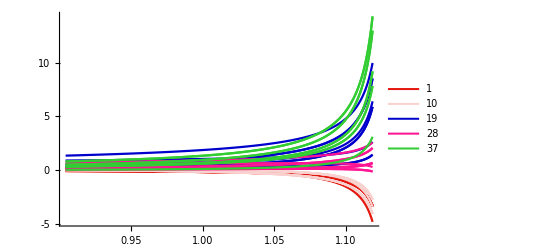
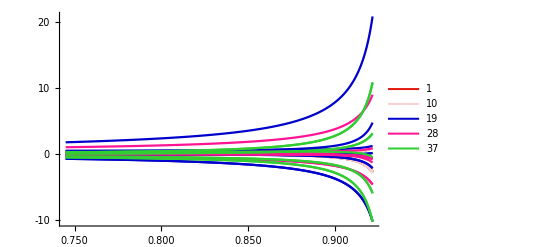
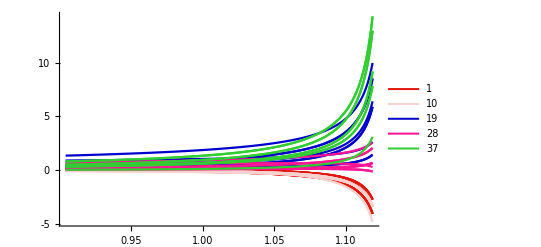

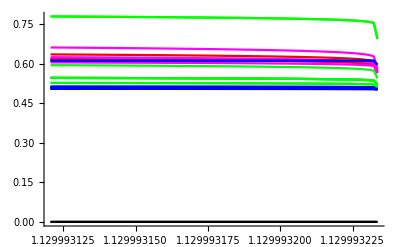
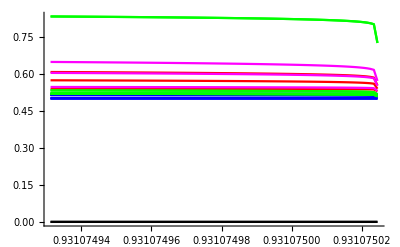
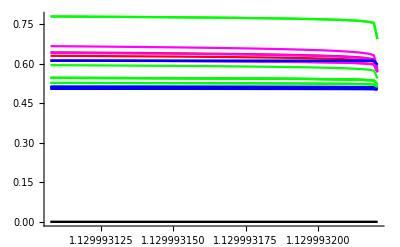

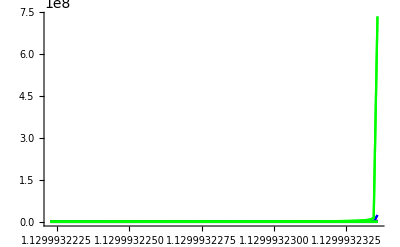
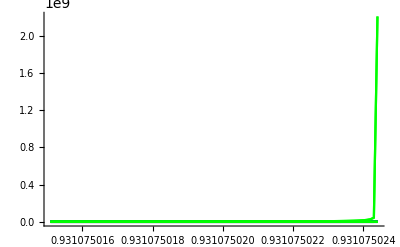

{{gIV0c0[t],gIV0c2[t]},{gIV0c0[t],gIV0c2[t],gIV2c1[t]},{gIV1c1[t]}}

{{χM0c0[t]},{χM1c1[t]},{χM1c0[t]}}

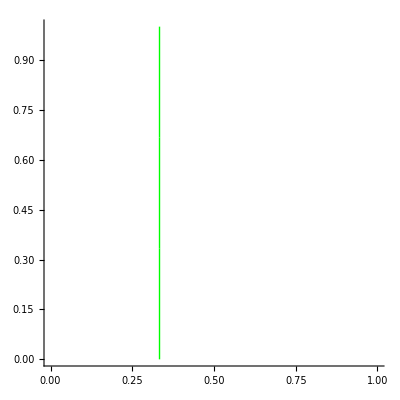

```mathematica
(*Plotting and analysis*)

SetOptions[LinTicks,MajorTickLength->{0.02,0},MinorTickLength->{0.013,0},MajorTickStyle-> Thickness[0.003],MinorTickStyle-> Thickness[0.003]];

singTripList=Join[Table[Abs[(D0L[[n+1]]+D0L[[Mod[-n,q]+1]])]/2,{n,0,q-1}],Table[Abs[(D0L[[n+1]]-D0L[[Mod[-n,q]+1]])]/2,{n,0,q-1}],Table[Abs[(D1L[[n+1]]+D1L[[Mod[-n-1,q]+1]])]/2,{n,0,q-1}],Table[Abs[(D1L[[n+1]]-D1L[[Mod[-n-1,q]+1]])]/2,{n,0,q-1}]];

vxPlots=List[];
ExpPlots=List[];
gPlotsL=List[];
χPlots=List[];
Dplots=List[];
DplotsDFT=List[];
DsingtripPlot=List[];
gMaxList=ConstantArray[0,q];
vxMaxList=ConstantArray[0,q];
χMaxList=ConstantArray[0,q];
vxListFinal=ConstantArray[0,q];
colorList=ConstantArray[0,q];
colorMap=Function[n,Which[n≤ 2q, Red,2q<n≤ 2q+q^2, Blue,2q+q^2<n≤ 2q+2q^2,Green,n> 2q+2q^2,Black]];
For[band=1,band≤ q,band++,
AppendTo[gPlotsL,Plot[Evaluate[Evaluate[Re[gList/.sols[[band]]]]],{t,0.8*domains[[band]],0.99domains[[band]]},PlotRange->All,PlotStyle->Join[ConstantArray[Directive[ColorData["Legacy"]["DeepCadmiumRed"],Thickness[0.004]],q^2] ,ConstantArray[Directive[Lighter[ColorData["Legacy"]["DeepCadmiumRed"],0.8],Thickness[0.004]],q^2] ,ConstantArray[Directive[ColorData["Legacy"]["MediumBlue"],Thickness[0.004]],q^2] ,ConstantArray[Directive[ColorData["Legacy"]["DeepPink"],Thickness[0.004]],q^2] ,ConstantArray[Directive[ColorData["Legacy"]["LimeGreen"],Thickness[0.004]],q^2] ,{Black,Black}], AxesStyle-> Directive[FontSize-> 30,Thickness[0.0015]],PlotLegends->Automatic,Ticks-> LinTicks]];

(*list of critical exponents*)
indexList=Flatten[Join[Table[D[D0L[[m+1]],t]/D0L[[m+1]]*( domains[[band]]-t),{m,0,q-1}],Table[D[D1L[[m+1]],t]/D1L[[m+1]]*(domains[[band]]-t),{m,0,q-1}],Table[D[RL[[m+1,n+1]],t]/RL[[m+1,n+1]]*(domains[[band]]-t),{m,0,q-1},{n,0,q-1}],Table[D[ML[[m+1,n+1]],t]/ML[[m+1,n+1]]*(domains[[band]]-t),{m,0,q-1},{n,0,q-1}]]];
AppendTo[ExpPlots,Plot[{Evaluate[Abs[Evaluate[1/2+1/2(Log[Abs[χvxList/.sols[[band]]]]/Log[1/(domains[[band]]-t)])/.sols[[band]]]]],0,0*1/2},{t,0.9999999*domains[[band]],domains[[band]]},PlotRange->All,PlotStyle->Join[ConstantArray[Red,q] ,ConstantArray[Magenta,q] ,ConstantArray[Blue,q^2] ,ConstantArray[Green,q^2] ,{Black,Black} ]]];

(*plot vertex flow*)
AppendTo[vxPlots,Plot[Evaluate[Abs[vxList/.sols[[band]]]],{t,0.99999999domains[[band]],domains[[band]]},PlotRange->All,PlotStyle->Join[ConstantArray[Red,q] ,ConstantArray[Magenta,q] ,ConstantArray[Blue,q^2] ,ConstantArray[Green,q^2] ,{Black,Black} ]]];
(*plot susceptibility flow*)
AppendTo[χPlots,Plot[Evaluate[Abs[χvxList/.sols[[band]]]],{t,0.99999999domains[[band]],domains[[band]]},PlotRange->All,PlotStyle->Join[ConstantArray[Red,q] ,ConstantArray[Magenta,q] ,ConstantArray[Blue,q^2] ,ConstantArray[Green,q^2] ,{Black,Black} ]]];
(*plot singlet/triplet parts of the pairing gaps*)
AppendTo[DsingtripPlot,Plot[Evaluate[singTripList/.sols[[band]]],{t,0.domains[[band]],0.99999domains[[band]]},PlotRange->All,PlotStyle-> Join[ConstantArray[Red,q] ,ConstantArray[Blue,q],ConstantArray[Magenta,q],ConstantArray[Cyan,q]]]];
(*determine largest exponent*)
gAbsList=Flatten[Abs[gList/.sols[[band]]]/.{t->0.9999999domains[[band]]}];
gMaxList[[band]]=gList[[Flatten[Position[gAbsList,Max[gAbsList]]]]];
χAbsList=Flatten[Evaluate[Abs[χvxList/.sols[[band]]]/.{t->domains[[band]]}]];
χMaxList[[band]]=χvxList[[Flatten[Position[χAbsList,Max[χAbsList]]]]];
colorList[[band]]=colorMap[Position[χAbsList,Max[χAbsList]][[1,1]]];


(*plot pairing gap function as a function of py in the BZ*)
AppendTo[Dplots,ListPlot[{Join[Table[{Mod[P[q,m,0][[2]],2Pi,-Pi],(Evaluate[Abs[D0L[[m+1]]/.sols[[band]]]][[1]]/Evaluate[Abs[D0L[[1]]/.sols[[band]]]][[1]])/. {t-> 0.999999domains[[band]]}},{m,0,q-1}],Table[{Mod[P[q,m,1][[2]],2Pi,-Pi],(Evaluate[Abs[D1L[[m+1]]/.sols[[band]]]][[1]]/Evaluate[Abs[D0L[[1]]/.sols[[band]]]][[1]])/. {t-> 0.999999domains[[band]]}},{m,0,q-1}]],Join[Table[{Mod[P[q,m,0][[2]],2Pi,-Pi],Evaluate[Arg[D0L[[m+1]]/.sols[[band]]]-Arg[D0L[[2]]/.sols[[band]]]][[1]]/. {t-> 0.999999domains[[band]]}},{m,0,q-1}],Table[{Mod[P[q,m,1][[2]],2Pi,-Pi],Evaluate[Arg[D1L[[m+1]]/.sols[[band]]]-Arg[D0L[[2]]/.sols[[band]]]][[1]]/. {t-> 0.999999domains[[band]]}},{m,0,q-1}]]},PlotStyle->PointSize[0.02]]];

]
Table[Show[gPlotsL[[j]]],{j,1,Length[gPlotsL]}]
Table[Show[ExpPlots[[j]]],{j,1,Length[ExpPlots]}]
Table[Show[vxPlots[[j]]],{j,1,Length[vxPlots]}]
Table[Show[χPlots[[j]]],{j,1,Length[vxPlots]}]
Table[Show[DsingtripPlot[[j]]],{j,1,Length[vxPlots]}]
Table[Show[Dplots[[j]]],{j,1,Length[Dplots]}]
Table[Show[DplotsDFT[[j]]],{j,1,Length[DplotsDFT]}]
gMaxList
(*vxMaxList*)
χMaxList
Graphics[Table[{colorList[[b+1]],Thick,Line[{{p/q,b/q},{p/q,(b+1)/q}}]},{b,0,q-1}],PlotRange->{{0,1},{0,1}}, Axes->True,AspectRatio->1]
```

```mathematica
Plot[Evaluate[Abs[χvxList/.sols[[1]]]/.{t->domains[[1]]+u 10^(-8)}],{u,(0.99999998-1)domains[[1]] 10^8,(0.9999999999-1)domains[[1]] 10^8},PlotRange->All,PlotStyle->Join[ConstantArray[Directive[ColorData["Legacy"]["DeepCadmiumRed"],Thickness[0.006]],q] ,ConstantArray[Directive[ColorData["Legacy"]["DeepPink"],Thickness[0.006]],q] ,ConstantArray[Directive[ColorData["Legacy"]["MediumBlue"],Thickness[0.006]],q^2] ,ConstantArray[Directive[ColorData["Legacy"]["LimeGreen"],Thickness[0.006]],q^2] ,{Black,Black} ],AxesStyle-> Directive[FontSize-> 30,Thickness[0.0015]],PlotLegends->Automatic,AxesOrigin->{(0.99999998-1)domains[[1]] 10^8,0},Ticks->LinTicks]
Plot[Evaluate[1/2+1/2(Log[Abs[χvxList/.sols[[1]]]]/Log[1/(domains[[1]]-t)])/.{t->domains[[1]]+u 10^(-8)}],{u,(0.99999998-1)domains[[1]] 10^8,0(0.999999999-1)domains[[1]] 10^8},PlotRange->All,PlotStyle->Join[ConstantArray[Directive[ColorData["Legacy"]["DeepCadmiumRed"],Thickness[0.006]],q] ,ConstantArray[Directive[ColorData["Legacy"]["DeepPink"],Thickness[0.006]],q] ,ConstantArray[Directive[ColorData["Legacy"]["MediumBlue"],Thickness[0.006]],q^2] ,ConstantArray[Directive[ColorData["Legacy"]["LimeGreen"],Thickness[0.006]],q^2] ,{Black,Black} ],AxesStyle-> Directive[FontSize-> 30,Thickness[0.0015]],PlotLegends->Automatic,AxesOrigin->{(0.99999998-1)domains[[1]] 10^8,0.5},Frame-> True,PlotRangePadding->0.02,FrameStyle-> Directive[FontSize-> 40,Thickness[0.0015]],FrameTicks->{{LinTicks,None},{LinTicks,None}}]
```

```mathematica
(* fourth order free energy analysis *)
```

```mathematica
(* bMN coefficients in Eq. (S36) for fourth order free energy analysis *)

βMNlist=ConstantArray[0,q];
For[band=1,band≤ q,band++,

βMNlist[[band]]=Table[Sum[(Conjugate[Δmn0[[Mod[m-l,q]+1,l+1]]]Δmn0[[Mod[m-l,q]+1,Mod[n-m+l,q]+1]]Conjugate[Δmn0[[Mod[-n-l,q]+1,Mod[n-m+l,q]+1]]]Δmn0[[Mod[-n-l,q]+1,Mod[l,q]+1]]/.sols[[band]])/.{t-> 0.9999 domains[[band]]},{l,0,q-1}]+Sum[(Conjugate[Δmn1[[Mod[m-l,q]+1,l+1]]]Δmn1[[Mod[m-l,q]+1,Mod[n-m+l,q]+1]]Conjugate[Δmn1[[Mod[-n-l,q]+1,Mod[n-m+l,q]+1]]]Δmn1[[Mod[-n-l,q]+1,Mod[l,q]+1]]/.sols[[band]])/.{t-> 0.9999 domains[[band]]},{l,0,q-1}],{m,0,q-1},{n,0,q-1}];
βMNlist[[band]]=(βMNlist[[band]]+Table[βMNlist[[band]][[Mod[m,q]+1,Mod[-n,q]+1]],{m,0,q-1},{n,0,q-1}])/2;
]
```

```mathematica
(* order parameters for fourth order free energy analysis *)
ηv={η0,η1,η2};
ηvΙ={ηΙ0,ηΙ1,ηΙ2};
```

```mathematica
(* fourth order free energy from Eq. (S35) *)
F=FullSimplify[Table[-100(ηv+I ηvΙ).(ηv-I ηvΙ)+Sum[Sum[βMNlist[[band]][[Mod[m,q]+1,Mod[n,q]+1]]/βMNlist[[band]][[1,1]]Sum[(ηv+I ηvΙ)[[Mod[L+m,q,1]]](ηv+I ηvΙ)[[Mod[L-m,q,1]]](ηv-I ηvΙ)[[Mod[L+n,q,1]]](ηv-I ηvΙ)[[Mod[L-n,q,1]]],{L,0,q-1}],{m,0,q-1}],{n,0,q-1}],{band,1,q}]];
```

```mathematica
(* minimizing fourth order free energy *)
Fmin=Table[NMinimize[Re[F[[band,1]]],{η0,η1,η2,ηΙ0,ηΙ1,ηΙ2},MaxIterations->200],{band,1,q}];
```

```mathematica
tab=Table[Fmin[[band,2]],{band,1,q}];
```

```mathematica
ListPlot[Table[Table[{band,(Abs[(ηv[[j]]+I ηvΙ[[j]])])/.tab[[band]]},{band,1,q,1}],{j,1,q}],PlotRange->{0,4.5}]
```

```mathematica
Show[ListPlot[Table[Table[{j,(Arg[(ηv[[j]]+I ηvΙ[[j]])]-Arg[(ηv[[1]]+I ηvΙ[[1]])])/.tab[[band]]},{band,3,3,1}],{j,1,q}],PlotRange->All],Plot[2Pi/3,{x,0,4}]]
```